# 医学生物学分野における高被引用論文の長期変化

天野晃

## 要旨

PubMedの3000万件を超える収録記事を対象として、高被引用論文を抽出、これにかかる雑誌や研究テーマの変遷、レファレンスネットワークの構造変化を75年間にわたり俯瞰する。

## 背景

論文を単位とした巨大レファレンスネットワークの分析は少なく、とくに長期間にわたる変化を捉えるものはさらに少ない。
短期的なインパクトを捉える指標はあるが分野全体に対して長期にわたりどのようなトレンドがあるか調査したものは少ない。

## 方法

### 1. データ

FTP版のPubmed baseline (2023)[8]を利用した。

### 2. 世代の構成

PubMedに収録されている出版年が1946-2020である論文を対象とした。経年変化を見るために1946-2020の出版年をオーバーラップなしの5年ごとの区切りとし、15層のレファレンスネットワークの世代を構成した。各世代で対象となる被引用論文はPubmed baselineに収録される最初の出版年（1781）から当該世代までのすべてのタイプの記事となる。これらを累積的に用いる場合には累積世代と称する。図表において各世代/累積世代を表す場合には最終年を表記する。

### 3. 主要論文・主要雑誌・主要テーマ

本研究においてはトレンドとして主要論文、主要雑誌、主要テーマに注目する。主要論文とは、本研究タイトルの「高被引用論文」のことであり、各累積世代において、被引用数上位の論文であり、全被引用数の1%を構成する論文集合とする。全被引用数1%に対する厳密な抽出は困難であるため、被引用数の多い順に論文を累積し、全被引用数の1%に最も近い順位を持つ論文までを対象とした。主要雑誌とは主要論文を出版した雑誌とする。主要テーマとは主要論文に付与されるNeSHおよび主要論文を引用する論文に付与されるNeSHの集合とする。

以上の定義を表1にまとめる。

表1

本研究での用語定義

主要論文 | 被引用数全体の1%を構成する被引用数上位論文（集合）。
主要雑誌 | 主要論文を出版した雑誌。
主要テーマ | 主要論文に付与されるMeSHおよびその論文を引用する論文に付与されるMeSH。
世代 | 1946 - 2020の期間に対して5年ごとに区切るもの。データを累積的に扱う場合は「累積世代」と表記する。

#### 3.1 主要テーマの計数

前述の通り主要テーマには引用される論文のテーマおよび引用する論文のテーマが定義される。これらの単独の計数についてはそれぞれ主要論文に付与されるMeSHディスクリプター、主要論文を引用する論文に付与されるMeSHディスクリプターを用いる。一方、引用関係の計数は以下のように行う。一対の論文の引用関係をディスクリプター集合間の引用関係ととらえ、これを被引用側・引用側における完全2部グラフの関係とみなしエッジを計数する。

## 結果

### 1. PubMed annual baseline

本研究で用いた2023年のFTP版PubMed annual baselineの概要を表2に示す。わずかに2024年の論文も含まれている。

表 2

PubMed annual baselineのレコード数

論文数 | 雑誌数 | 最初の論文出版年 | 最後の論文出版年
36,555,430 | 36,943 | 1781 | 2024

出版年ごとの論文収録数を図1に示す。1945年から明確な増加が見られる。

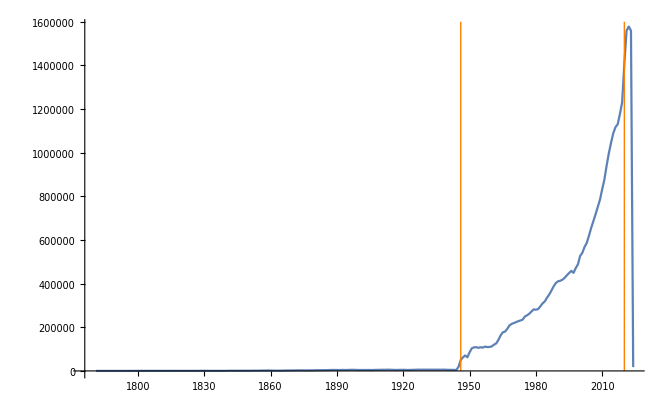

図1

PubMed annual baselineの登録論文数の推移

### 2. 世代ごとの論文数

世代ごとの論文数、うち参照を持つ論文数、参照数（述べ）、被引用論文数（ユニーク）、登録雑誌数を図2に示す。登録雑誌数以外は2005から2010にかけ急激な指数関数的増加を示している。

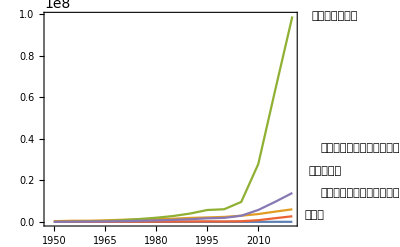

図 2

世代ごとの論文数

累積世代ごとの被引用数とそのランクを、Zipfの式 [c r^(-a)] に回帰させた場合の係数aの推移を図3に示す。係数aは1946-1980の世代をピークに前半では上昇傾向、後半では下降傾向にある。いずれの値も1未満であり学術活動に一般的に見られる冪乗則における値よりも小さい。

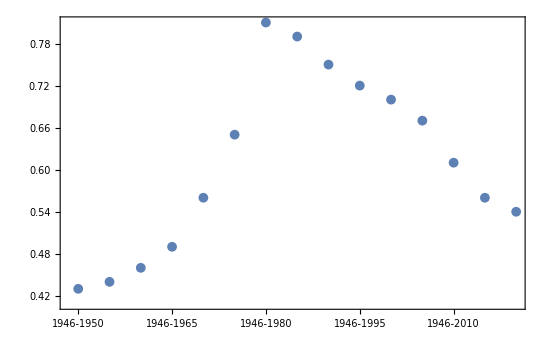

図3

累積世代ごとの被引用数におけるZipfの係数aの値

### 3. 累積世代ごとの主要論文の変化

主要論文の新規出現数を表3に示す。主要論文における新規論文の出現は一定でなく増減における傾向も見られない。2006から2020の3世代では主要論文数そのものが急増しているが、これは収録論文数の急増を受けてのものであると考えられる。

表3

累積世代ごとの主要論文および新規主要論文の出現数

Generation | Newcomer | Newcomer % | Top 1% article
1946-1950 | - | - | 10
1946-1955 | 22 | 73. | 30
1946-1960 | 25 | 54. | 46
1946-1965 | 20 | 40. | 50
1946-1970 | 9 | 24. | 38
1946-1975 | 7 | 21. | 33
1946-1980 | 8 | 25. | 32
1946-1985 | 10 | 38. | 26
1946-1990 | 2 | 11. | 19
1946-1995 | 5 | 23. | 22
1946-2000 | 6 | 18. | 33
1946-2005 | 27 | 41. | 66
1946-2010 | 123 | 64. | 192
1946-2015 | 158 | 50. | 315
1946-2020 | 104 | 31. | 336

累積世代ごとの最多被引用論文の論文タイトルとその被引用数を表4に示す。主要論文は世代が進んでも引き続き引用され続ける傾向があり最多被引用主要論文の交代は少ない。いずれの論文のテーマもタンパク質の分析に関するものであり、後者2タイトルは出版後10年から数十年をかけてインパクトを上昇させている。

表4

累積世代ごとの最多被引用論文タイトル

Generation | Article title | Journal | Publish year | cited count
1946-1950 | Qualitative analysis of proteins: a partition chromatographic method using paper | Biochem J. | 1944 | 74
1946-1955 | Qualitative analysis of proteins: a partition chromatographic method using paper | Biochem J. | 1944 | 154
1946-1960 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 300
1946-1965 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 1190
1946-1970 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 3876
1946-1975 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 9632
1946-1980 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 17763
1946-1985 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 25451
1946-1990 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 32371
1946-1995 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 37576
1946-2000 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 40229
1946-2005 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 42101
1946-2010 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 44884
1946-2015 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4 | Nature. | 1970 | 49961
1946-2020 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4 | Nature. | 1970 | 54249

### 4. 累積世代ごとの主要雑誌の変化

累積世代ごとの主要雑誌のうち主要論文出版数上位の一覧を表5に示す。主要論文を持つ雑誌は必ずしもインパクトファクターが高い雑誌ではないことがわかる。

表5

累積世代ごとの主要雑誌のうち主要論文の最大出版数を持つもの：
インパクトファクター(IF)とその発表年については当該誌の公式ホームページから求めた。

Generation | Journal title (article count) IF / IFyear | Top 1% Journal
1946-1950 | The journal of clinical investigation | (3) | 13.3 | / | 2023
Biochemical journal | (3) | 4.4 | / | 2023 | 5
1946-1955 | Biochemical journal | (13) | 4.4 | / | 2023 | 11
1946-1960 | Biochemical journal | (11) | 4.4 | / | 2023 | 19
1946-1965 | Biochemical journal | (13) | 4.4 | / | 2023 | 16
1946-1970 | Biochemical journal | (9) | 4.4 | / | 2023 | 14
1946-1975 | The Journal of biological chemistry | (7) | 4. | / | 2023 | 18
1946-1980 | The Journal of biological chemistry | (7) | 4. | / | 2023 | 20
1946-1985 | The Journal of biological chemistry | (5) | 4. | / | 2023 | 17
1946-1990 | The Journal of biological chemistry | (4) | 4. | / | 2023 | 12
1946-1995 | The Journal of biological chemistry | (4) | 4. | / | 2023 | 13
1946-2000 | Journal of Molecular Biology | (4) | 4.7 | / | -
Proceedings of the National Academy of Sciences of the United States of America | (4) | 9.4 | / | 2023 | 19
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | (8) | 9.4 | / | 2023 | 28
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America | (14) | 9.4 | / | 2023
Nature | (14) | 50.5 | / | 2023 | 83
1946-2015 | Nature | (20) | 50.5 | / | 2023 | 136
1946-2020 | Bioinformatics | (17) | 4.4 | / | 2023 | 145

### 5. 累積世代ごとの主要テーマの変化

#### 5.1 主要論文のテーマの変化

主要論文に付与されたMeSHディスクリプターを表6に示す。ディスクリプターの出現が多いため表には出現数上位10%を占める出現数上位のディスクリプターのみ記載した。上位ディスクリプター全体で見た場合、世代が累積的であるのでトレンドがやや遅れ気味に見られる。たとえば”Genetic”や”DNA”といったゲノム科学に関するタームの出現は1980世代より見られる。一方で他分野のテーマを表すディスクリプターの出現も見られる。例えば”Internet”や”Software”といった情報学分野である。新しい世代ではより詳細なテーマを示すターム、たとえば”China”や”COVID-19”といったタームの出現が著しい。

表6

累積世代ごとの主要論文に付与されたMeSHディスクリプターの出現頻度上位のもの

Generation | Top 10% descriptor from Top 1% MeSH
 {Descriptor, count} | Top 10% newcomer from Top 1% MeSH
 {Descriptor, count} | Top 1% MeSH count
 Newcomer/All
1946-1950 | {} | {} | 0/0
1946-1955 | {{Humans/290}} | {{Humans/290}} | 45/45
1946-1960 | {{Humans/797},{Proteins/640}} | {{Electrons/503}} | 61/96
1946-1965 | {{Microscopy, Electron/1811},{Proteins/1789}} | {{Staining and Labeling/785}} | 42/117
1946-1970 | {{Microscopy, Electron/5006},{Proteins/4744}} | {{Research/468},{Leukocytes/311}} | 33/122
1946-1975 | {{Proteins/11363},{Molybdenum/9632}} | {{Acrylates/725},{Chemical Phenomena/725}} | 21/125
1946-1980 | {{Proteins/21821},{Molybdenum/17763}} | {{Genes/2995}} | 44/137
1946-1985 | {{Proteins/33413},{Molybdenum/25451}} | {{DNA Restriction Enzymes/6706},{DNA-Directed DNA Polymerase/4887}} | 55/143
1946-1990 | {{Proteins/42099},{Molybdenum/32371},{Phenols/32371}} | {{Methionine/2840}} | 9/108
1946-1995 | {{Proteins/53210},{Base Sequence/50402},{Coliphages/49230}} | {{Conjugation, Genetic/3927},{Genetic Vectors/3927},{Methylation/3927}} | 30/128
1946-2000 | {{Base Sequence/66991},{Proteins/65865},{Animals/60982}} | {{Amino Acid Sequence/6743},{Operon/5573},{Nucleic Acids/5171},{Temperature/4957}} | 71/199
1946-2005 | {{Animals/90572},{Base Sequence/89147},{Proteins/86356}} | {{Molecular Sequence Data/13379},{Sequence Alignment/9318},{Centrifugation, Density Gradient/4303},{Protein Structure, Secondary/4300}} | 126/325
1946-2010 | {{Humans/158560},{Animals/155701},{Proteins/133209},{Base Sequence/123202}} | {{Female/24979},{Sequence Analysis, DNA/20733},{Adult/19465},{Middle Aged/17273},{Internet/16645},{Crystallography, X-Ray/14683},{Evolution, Molecular/14640},{Aged/14540}} | 550/875
1946-2015 | {{Humans/528325},{Animals/303404},{Software/232535},{Proteins/190391}} | {{Software Design/16245},{Sequence Analysis, RNA/15708},{Meta-Analysis as Topic/14949},{Fibroblasts/14388},{Registries/13736},{Magnetic Resonance Imaging/13212},{DNA-Binding Proteins/13109},{Research Design/12463},{Stem Cells/12199},{Image Processing, Computer-Assisted/11710},{Octamer Transcription Factor-3/10931},{Pluripotent Stem Cells/10931}} | 468/1243
1946-2020 | {{Humans/1150488},{Software/599982},{Algorithms/487149}} | {{China/37829},{Coronavirus Infections/31960},{COVID-19/31960},{Pneumonia, Viral/31960},{Liver Neoplasms/20869}} | 217/1178

累積世代ごとの主要論文に付与されたMeSHディスクリプターの種数を図4に示す。後半の世代では種数が減少傾向にあり、主要論文におけるテーマの分散が見られる。

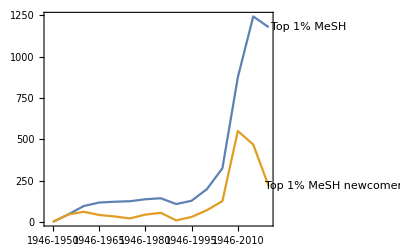

図4

累積世代ごとの主要論文に付与されたMeSHディスクリプターの種数

主要論文に付与されたMeSHディスクリプターの出現数に関して、世代ごとのジニ係数を図5に示す。ジニ係数には上昇傾向が見られることから特に関心が持たれるテーマに関しては年々集中する傾向がある可能性を示している。

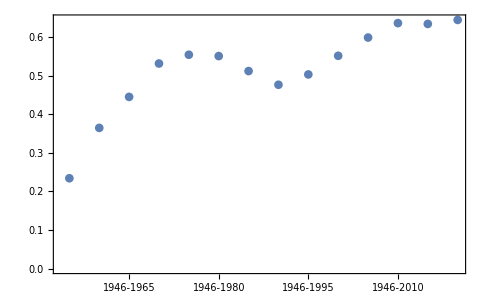

図5

累積世代ごとの主要論文に付与されたMeSHディスクリプターの出現数に関するジニ係数

#### 5.2 主要論文を引用する論文のテーマの変化

主要論文を引用する論文に付与されたMeSHディスクリプターを表7に示す。ディスクリプターが大規模であるため出現数（引用数）上位10%のものを記載した。ディスクリプターの種数としては主要論文のものと比べ相当多く（主要論文のものの数倍）、高被引用となるテーマは他のざまざまなテーマから引用されるであろうという直観と一致する。新規出現するディスクリプターも同様の傾向が見られる。表6と表7より出現数上位となるディスクリプターを比較すると、表7がより分野の広さを反映している傾向は見られるものの、かなり一般的な”Humans”や”Animals”といったディスクリプターが多見される特徴は同様である。

表7

累積世代ごとの主要論文を引用する論文に付与されたMeSHディスクリプターの出現頻度上位のもの

Generation | Top 10% descriptor from Top 1% MeSH
 {Descriptor, count} | Top 10% newcomer from Top 1% MeSH
 {Descriptor, count} | Top 1% MeSH count
 Newcomer/All
1946-1950 | {} | {{Humans/112}} | 434/434
1946-1955 | {{Humans/612},{Animals/282}} | {{Electrophoresis/79},{Brain/60},{Electrophoresis, Paper/41},{Carbohydrate Metabolism/39},{Polysaccharides/27},{Muscle Relaxants, Central/25},{Cerebrovascular Circulation/24},{Nucleotides/23},{Epinephrine/21}} | 1193/1596
1946-1960 | {{Humans/1499},{Animals/1282}} | {{Endoplasmic Reticulum/121},{Cell Membrane/82},{Golgi Apparatus/74},{Epithelium/40},{Synapses/39},{Vacuoles/30},{Capillaries/28}} | 1484/3000
1946-1965 | {{Animals/3098},{Humans/2091},{Research/1618}} | {{Carbon Isotopes/135},{RNA, Bacterial/90},{DNA, Bacterial/88},{Ultracentrifugation/86},{Toxicology/70},{Immunodiffusion/57},{Virus Cultivation/49},{Haptoglobins/45}} | 1789/4537
1946-1970 | {{Animals/7661},{Microscopy, Electron/5030},{Humans/3387}} | {{Methods/484}} | 1325/5547
1946-1975 | {{Animals/14885},{Microscopy, Electron/8076},{Humans/5825},{Rats/4854},{Male/4735}} | {{Sodium Dodecyl Sulfate/375},{Ammonium Sulfate/312},{Immunoglobulin A/274},{Nitrosoguanidines/183}} | 1799/7102
1946-1980 | {{Animals/24280},{Microscopy, Electron/9168},{Humans/9159},{Male/8239},{Rats/8158}} | {{DNA, Recombinant/311},{Cell Transformation, Viral/251},{Membrane Lipids/212}} | 1809/8710
1946-1985 | {{Animals/37847},{Humans/15663},{Rats/12245},{Male/11631},{Molecular Weight/9837}} | {{Genes, Fungal/582},{Oncogenes/525},{Promoter Regions, Genetic/412}} | 1790/10114
1946-1990 | {{Animals/56371},{Humans/26871},{Base Sequence/23263},{Rats/17104},{Cloning, Molecular/15633}} | {{Blotting, Western/1526}} | 1708/11617
1946-1995 | {{Animals/81925},{Base Sequence/52007},{Molecular Sequence Data/45030},{Humans/43467}} | {{DNA Primers/2187}} | 2485/14061
1946-2000 | {{Animals/110647},{Base Sequence/73355},{Molecular Sequence Data/69604},{Humans/61491}} | {{Reverse Transcriptase Polymerase Chain Reaction/657}} | 1656/15717
1946-2005 | {{Animals/149442},{Molecular Sequence Data/105483},{Base Sequence/101038},{Humans/88078}} | {{Databases, Genetic/487},{Databases, Nucleic Acid/216},{Proteomics/210}} | 2306/18023
1946-2010 | {{Animals/238925},{Humans/200639},{Molecular Sequence Data/170368},{Base Sequence/139338}} | {{Quality of Life/2604},{Genome-Wide Association Study/1398},{Activities of Daily Living/1083},{Gene Regulatory Networks/928},{Depressive Disorder, Major/774},{Geriatric Assessment/661}} | 4936/22959
1946-2015 | {{Humans/544356},{Animals/401241},{Female/257601},{Male/248540}} | {{Exome/2967},{Neoplasm Grading/2513},{Gene Ontology/2363}} | 3186/26120
1946-2020 | {{Humans/1032160},{Animals/594100},{Female/524201}} | {{COVID-19/24342}} | 2022/28061

主要論文を引用する論文に付与されたMeSHディスクリプターの種数を図6に示す。引用される論文のそれに比べ種数は多く、かつ一定の上昇傾向にあり、急激な上昇などは見られない。新規ディスクリプターは毎世代を通して一定に出現している。

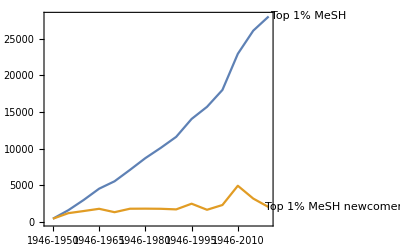

図6

累積世代ごとの主要論文を引用する論文に付与されたMeSHディスクリプターの種数

主要論文を引用する論文に付与されたMeSHディスクリプターの出現数に関して、世代ごとのジニ係数を図7に示す。ジニ係数には主要論文のそれと同じ上昇傾向が見られる。

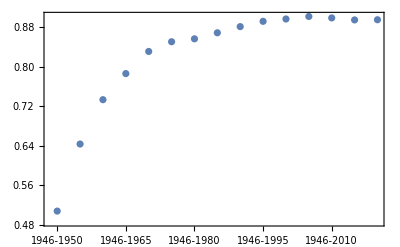

図7

累積世代ごとの主要論文を引用する論文に付与されたMeSHディスクリプターの出現数に関するジニ係数

#### 5.3 主要論文のテーマと主要論文を引用する論文のテーマの差異

累積世代ごとの主要論文のMeSHディスクリプタ数と、主要論文を引用する論文のMeSHディスクリプタ数の比を図8に示す。2010年以降は主要論文に付与されるディスクリプター数の比が高くなっており相対的な主要テーマの広がりを示している。

表8

累積世代ごとの主要論文にのみ出現するMeSHディスクリプタ

累積世代 | 主要論文にのみ見られるディスクリプター
1946-1950 | 
1946-1955 | Capillaries
Tungsten Compounds
1946-1960 | Tungsten Compounds
1946-1965 | Tungsten Compounds
1946-1970 | Rare Diseases
Tungsten Compounds
1946-1975 | Rare Diseases
Thiobarbiturates
Tungsten Compounds
1946-1980 | Film Dosimetry
Tungsten Compounds
1946-1985 | Film Dosimetry
Nuclear Receptor Subfamily 4, Group A, Member 2
1946-1990 | Nuclear Receptor Subfamily 4, Group A, Member 2
1946-1995 | 
1946-2000 | Film Dosimetry
1946-2005 | Film Dosimetry
1946-2010 | 
1946-2015 | 
1946-2020 |

主要論文のテーマにのみ見られるディスクリプターもいくらか存在し、これを表8に示す。”Tungsten”といった材料に関するもの、”Dosimetry”といった線量測定に関するものが多い。

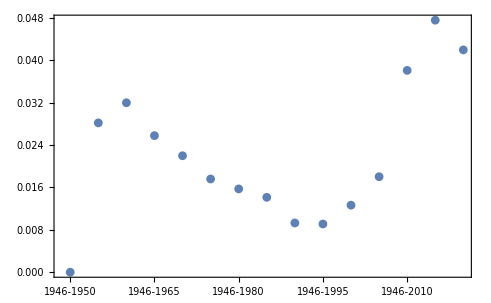

図8

累積世代ごとの主要論文のMeSHディスクリプタ種数と主要論文を引用する論文のMeSHディスクリプタ種数の比

全ての世代を通して出現するディスクリプターも存在し、主要論文においては8ターム（0.5%）、主要論文を引用する論文においては339ターム（1.2%）であった。

#### 5.4 主要論文とこれを引用する論文のテーマの引用関係

累積世代ごとの主要論文とそれを引用する論文の引用関係をMeSHディスクリプタの引用関係に置き換え、その変化を捉える。当該の関係のうち、上位25%の被引用を構成するMeSHディスクリプターによるネットワークを図9に示す。

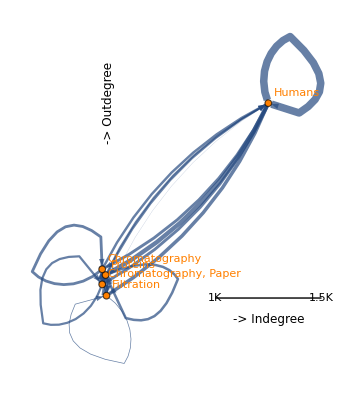
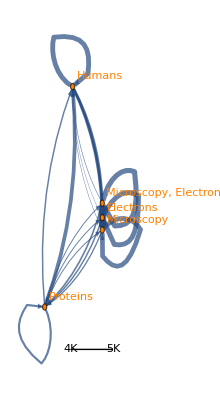
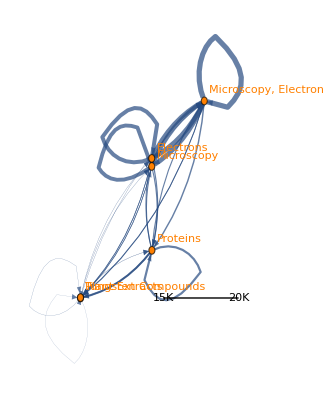
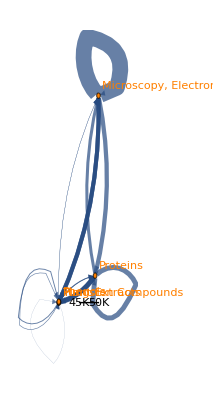
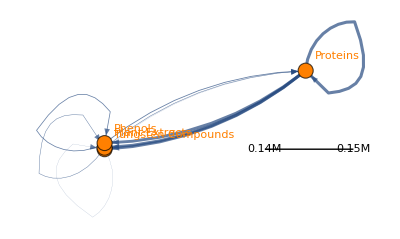
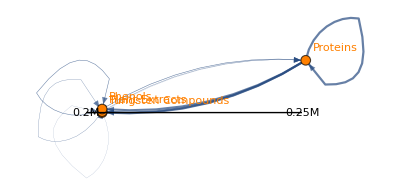
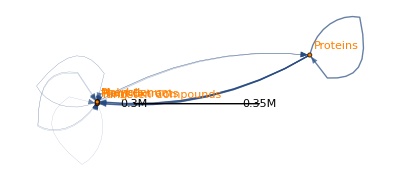
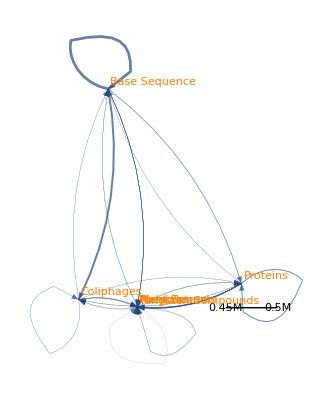
1946 - 1955 | -Graphics-
1946 - 1960 | -Graphics-
1946 - 1965 | -Graphics-
1946 - 1970 | -Graphics-
1946 - 1975 | -Graphics-
1946 - 1980 | -Graphics-
1946 - 1985 | -Graphics-
1946 - 1990 | -Graphics-
1946 - 1995 | -Graphics-
1946 - 2000 | -Graphics-
1946 - 2005 | -Graphics-
1946 - 2010 | -Graphics-
1946 - 2015 | -Graphics-
1946 - 2020 | -Graphics-

図9

累積世代ごとの主要論文とそれを引用する論文のMeSHディスクリプターの関係（上位25%の被引用）

### 6. 累積世代ごとのレファレンスネットワークの変化と主要論文の寄与

#### 6.1 累積世代ごとのレファレンスネットワーク構造の変化

ここではレファレンスネットワーク構造の変化を計量的に観察する。レファレンスネットワークの構造として想定されるものは、下位分野に対応するいくつかのサブネットワークの構成である。サブネットワークに該当する構造として弱連結グラフ（Weakly connected graph: WCG）を利用する。弱連結グラフとは共引用もしくは書誌結合によって連結される論文集合である。

累積世代ごとのWCGに関する各特徴量を表9にを示す。この表のはレファレンス情報をもとに構成しているため、レファレンスを持たず引用もされない論文は集計されていない。そこで「Largest WCG vertices % (all articles)」には全論文から再計算した割合を示す。Zipfの係数aについても全論文から再計算したがほぼ変化が見られなかったため記載していない。
全体の傾向として累積世代が進むに伴いWCGの数も増加するが最大WCGのメンバー数も急増する。この相乗効果によりグループを構成するメンバー数の差はより顕著になる。このことはZipfの係数aが累積世代が進むごとに増加していることからもわかる。一方で最大WCGのサイズ（論文数）も累積世代が進むにつれ増加し、2020にはそのメンバー数は全論文の6割に達している。

表9

累積世代ごとのレファレンスネットワークの属性:

論文数、WCG数、最大WCGにおける論文数（そのパーセンテージ）、すべての論文を対象にした場合の最大WCGにおける論文数のパーセンテージ、WCGを構成する論文数におけるZipfの係数a。

Generation | WCG | WCG vertices | Lone vertices | Largest WCG vertices | Largest WCG vertices % | Largest WCG vertices % (all articles) | Zipf's a
1946-1950 | 2353 | 25659 | 296336 | 17910 | 69.8 | 5.4 | 7.51
1946-1955 | 3851 | 106865 | 774662 | 94830 | 88.7 | 10.9 | 11.26
1946-1960 | 4624 | 230664 | 1203519 | 216474 | 93.8 | 15.3 | 12.1
1946-1965 | 5729 | 387646 | 1774556 | 370660 | 95.6 | 17.3 | 13.4
1946-1970 | 7020 | 635815 | 2542940 | 615244 | 96.8 | 19.5 | 13.94
1946-1975 | 8446 | 991194 | 3356424 | 966113 | 97.5 | 22.3 | 13.13
1946-1980 | 9401 | 1452803 | 4248958 | 1425267 | 98.1 | 25.1 | 13.7
1946-1985 | 10026 | 2022734 | 5222321 | 1993398 | 98.5 | 27.6 | 14.18
1946-1990 | 10687 | 2761367 | 6403037 | 2730892 | 98.9 | 29.9 | 14.7
1946-1995 | 11361 | 3715190 | 7594669 | 3683220 | 99.1 | 32.7 | 15.4
1946-2000 | 12147 | 4704818 | 9000206 | 4670358 | 99.3 | 34.2 | 15.4
1946-2005 | 13000 | 6388248 | 10294609 | 6351561 | 99.4 | 38.2 | 17.27
1946-2010 | 13398 | 9604916 | 10857321 | 9568400 | 99.6 | 46.9 | 17.87
1946-2015 | 13643 | 14351433 | 11071404 | 14315982 | 99.8 | 56.4 | 18.64
1946-2020 | 14933 | 20271870 | 11229183 | 20235562 | 99.8 | 64.4 | 19.1

#### 6.2 レファレンスネットワークの成長の様相

ここでは累積世代間のネットワークの差分を見ることにより、レファレンスネットワークの成長を捉える。成長をノードの発生、エッジの発生、これらによるネットワーク全体の構造変化ととらえ、構造変化に関してはWCGの結合に注目する。

##### 6.2.1 世代間で新たに発生した引用関係とこれにより結合されるWCG

6.2に挙げた項目の調査結果を表9に示す。新規に発生する引用やWCGの結合に寄与する論文は出版される論文の増加にともない増加する傾向にある。一方、他のWCGと結合されるWCGの割合は幅があるものの一定の傾向を見せている。

表9

累積世代間のレファレンスネットワークの差分に関する属性

累積世代 | 新規に発生した引用数 | 新規に発生した引用のうち
主要論文に対する引用数(%) | 新規に発生した引用に関して
異なる前世代WCGを結合する論文の数 | 新規に発生した引用により
結合が発生した前世代WCG数 | 新規に発生した引用により
異なる前世代WCGと結合された前世代WCG数 | 前世代WCG数 | WCGの結合率
1955 | 148555 | 718 (0.5) | 1632 | 1280 | 909 | 2353 | 0.39
1960 | 291655 | 3109 (1.1) | 1942 | 1485 | 1185 | 3851 | 0.31
1965 | 445022 | 8846 (2.) | 1717 | 1297 | 1070 | 4624 | 0.23
1970 | 818629 | 26986 (3.3) | 1937 | 1411 | 1133 | 5729 | 0.2
1975 | 1369688 | 43178 (3.2) | 2240 | 1549 | 1306 | 7020 | 0.19
1980 | 1998678 | 54563 (2.7) | 2520 | 1716 | 1500 | 8446 | 0.18
1985 | 2821649 | 103101 (3.7) | 2480 | 1683 | 1478 | 9401 | 0.16
1990 | 4022714 | 230540 (5.7) | 2438 | 1553 | 1392 | 10026 | 0.14
1995 | 5715688 | 221170 (3.9) | 2345 | 1450 | 1310 | 10687 | 0.12
2000 | 6095490 | 153837 (2.5) | 1603 | 1147 | 1048 | 11361 | 0.09
2005 | 9616785 | 103356 (1.1) | 2553 | 1508 | 1353 | 12147 | 0.11
2010 | 27854672 | 221562 (0.8) | 6243 | 2576 | 2407 | 13000 | 0.19
2015 | 63696093 | 1530822 (2.4) | 11124 | 3404 | 3235 | 13398 | 0.24
2020 | 98878679 | 5603859 (5.7) | 11676 | 3472 | 3255 | 13643 | 0.24

## 参考

Leydesdorf, L. Various methods for the mapping of science. Scientometrics. 1987, Vol. 11, Nos 5-6, p. 295-324.

Leydesdorf, L. Clusters and maps of science journals based on bi-connected graphs in Journal Citation Reports. Journal of Docu- mentation. 2004, Vol. 60, No. 4, p. 371-427.

Leydesdorf, L. Indicators of structual change in the dynamics of science: Entropy statisitics of the SCI Journal Citation Re- ports. Scientometrics. 2002, Vol. 53, No. 1, p. 131-159.

Leydesdorf L. Can scientific journals be classified in terms of aggregated journal- journal citation relations using the Journal Citation Reports? Journal of the American Society for Information Science and Tech- nology. 2006, Vol. 57, No. 5, p. 601-613.

天野晃;児玉閲;柴田大輔;小野寺夏生. 引用データに基づく自然科学領域における学術研究分野間の関係. 情報メディア研究. 2013, Vol 12, No. 1, p. 28-41.

天野晃;児玉閲. 引用にもとづく雑誌クラスタリング法の開発. 情報メディア研究. 2008, Vol 7, No. 1, p. 63-73.

Li

https://pubmed.ncbi.nlm.nih.gov/ . (accessed 2024.07.01)

## 検討

Essential journalsの過去のIF <- 困難

Clustering -> 可視化が困難なのでクラスタリングで工夫するしかない

article <- 困難かも

cited/citing -> modularityによるコミュニティ発見はできるかも

MeSH

journal

cited/citing

MeSH

MeSH

article cited/citing

article内共出現

Network構造分析

Networkにおけるcentralityの偏り

Network成長の可視化 (reference) <- なんらかの捨象・クラスタリングが必要 -> 難しい

article

Journal

MeSH

Essential articlesが構成する「Essential network」を抽出できるか？

グラフ(vertex)の差分に注目する

top 1%を元にネットワークを再構築する

メンバーのtop1%を考慮する

表6、7のタームの頻度を考慮する

ジニ計数 : 集中度がサチるので、別の指標の方がよい、尖度が良いか？

グラフ複雑性

graphRedundancyComplexity[g_Graph] := Module[{vc, ec, ecmean, etp},
  vc = VertexCount[g] // N;
  ec = EdgeCount[g] // N;
  ecmean = ec/(vc^2);
  etp = Entropy[AdjacencyMatrix[g] // Flatten] // N;
  (vc) (vc^ecmean) Exp[etp]
  ]